## gaussian beam propagation

```mathematica
(* beams sizes reported as either ISO 4σ diameters (divide by 3.03 to get waist) or 2w diameters (divide by 2 to get waist) [all measurements in mm] *)
```

```mathematica
gapMatrix[d_]:={{1,d},{0,1}}
thinLensMatrix[f_]:={{1,0},{-1/f,1}}
propagate[qInit_,system_]:=(system[[1,1]]*qInit+system[[1,2]])/(system[[2,1]]*qInit+system[[2,2]])
rayleigh[q_]:=Im[q]
waist[q_]:=Sqrt[rayleigh[q]*770*^-6/Pi]
zwaist[q_]:=-Re[q]
width[z_,z0_,w0_]:=w0*Sqrt[1+((z-z0)/(Pi w0^2/(770*^-6)))^2];
width[z_,q_]:=Sqrt[-1/(Im[1/(q+z)]Pi/770*^-6)]
(* give a system spec in the form {{ABCD1,gap1},{ABCD2,gap2},...} *)
beamPropagate[qInit_,spec_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[spec],i++,
element=spec[[i]];
qNext=propagate[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{width[x-z,qNext],z<x&&x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
];
Print[Plot[plots,{x,0,z},PlotRange->{0,All},Frame->True]];
q
]
beamPropagateLog[qInit_,spec_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[spec],i++,
element=spec[[i]];
qNext=propagate[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{width[x-z,qNext],z<x&&x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
];
Print[LogPlot[plots,{x,0,z},PlotRange->All,Frame->True]];
q
]
beamPlot[qInit_,spec_]:=Module[{q=qInit,qNext,plots={},i,element,z=0,zNext,x},
For[i=1,i≤Length[spec],i++,
element=spec[[i]];
qNext=propagate[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[plots,Piecewise[{{width[x-z,qNext],z<x&&x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
];
Plot[plots,{x,0,z},PlotRange->{0,All},Frame->True]
]
```

## From SHG cavity

horizontal axis Rayleigh length: 2.43086

vertical axis Rayleigh length: 2.43086

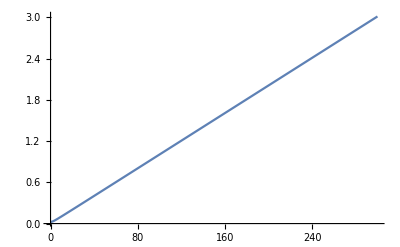

-Graphics-

```mathematica
Clear[z,x,z0,w0,xwaists,ywaists,sol1,sol2,limits,lr1,lr2]
sol={w0->0.024409,z0->0};
sol1=sol;
sol2=sol;
lr1=N[Pi*w0^2/770*^-6/.sol1];
Print["horizontal axis Rayleigh length: ",lr1]
lr2=N[Pi*w0^2/770*^-6/.sol2];
Print["vertical axis Rayleigh length: ",lr2]

limits={0,300};
Plot[width[x,z0,w0]/.sol1,{x,limits[[1]],limits[[2]]},PlotRange->{limits,{0,All}}]
Plot[width[x,z0,w0]/.sol2,{x,limits[[1]],limits[[2]]},PlotRange->{limits,{0,All}}]
```

## Beam shaping to mode-match well to the fiber, after the AOM.

```mathematica
Constraints
1) Fiber :OZ Optics PMJ-3A3A-633-4/125-3-5-1, MFD ~ 4 um. Aiming for waist of ~ 2um.
```

```mathematica
wfiber=2 10^-6;
w0=24.4 10^-6;
f1=150 10^-3;
f2=330 10^-3;
f3=300 10^-3;
f4=7.5 10^-3;
Print[(wfiber/w0)*( f1/f4)]

Clear[q1,q2,q1Predict,q2Predict]

q1=-(z0/.sol1)+I*lr1
q2=-(z0/.sol2)+I*lr2
```

1.63934

0.+2.43086 ⅈ

0.+2.43086 ⅈ

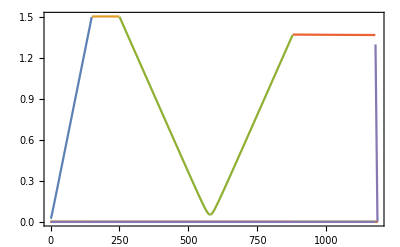

0.000308552+0.00734037 ⅈ

```mathematica
beamPropagate[q1,{{IdentityMatrix[2],10^3 f1},{thinLensMatrix[10^3 f1],100},{thinLensMatrix[10^3 f2],10^3(f2+f3)},{thinLensMatrix[10^3 f3],10^3 f3},{thinLensMatrix[10^3 f4],10^3 f4}}]
```

```mathematica
p
```

p

```mathematica
11.07/7.5
```

1.476